### The effective Hamiltonian of the Rabi model

Data are imported from julia code https : // github . com/djuliannader/RabiModel

```mathematica
R=50; (*quibit frequency*)
H[q_,p_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*g*q+λ)^2)^(1/2);
V[q_,gg_,λλ_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q+λλ)^2)^(1/2);
```

#### Normal phase

```mathematica
g=1/2^(1/2); (*coupling*)
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst]}],{en,-0.499,-0.2,0.0001}];
```

```mathematica
datarho={{-24.785295781452923 ,1.4007243413866022},
{-24.068100210624817, 1.3879736008885406},
{-23.344618023816295, 1.3764822425963972},
{-22.615353180960295, 1.366045365470574},
{-21.880738361413908, 1.3565032612764056},
{-21.141149162288382, 1.3477291118177988},
{-20.396914722766667, 1.3396206022209851},
{-19.64832584313539, 1.3320940424335288},
{-18.895641302204275, 1.3250801472628997},
{-18.139092850428852, 1.318520943607222},
{-17.37888921088487, 1.31236746217484},
{-16.615219324408613, 1.3065779867518388},
{-15.848255010348758, 1.3011167071344774},
{-15.07815316947822, 1.295952669192028},
{-14.305057623929123 ,1.2910589469331348},
{-13.529100666256907 ,1.286411982685183},
{-12.75040437313228 ,1.2819910561475147},
{-11.96908172686851, 1.2777778533494148},
{-11.185237578777562, 1.2737561138620763},
{-10.398969481352655, 1.269911339865452},
{-9.610368410910553, 1.2662305545654253},
{-8.819519398171444, 1.2627021002780305},
{-8.026502081001123, 1.2593154686549726},
{-7.231391190976164, 1.256061157125433},
{-6.434256983392627, 1.252930546868059},
{-5.635165618705985, 1.2499157985726823},
{-4.834179502069345, 1.2470097629769448},
{-4.031357586567619, 1.2442059037584927}};
dataT=Table[{datarho[[i,1]]/R,2π*datarho[[i,2]]},{i,1,20}];
```

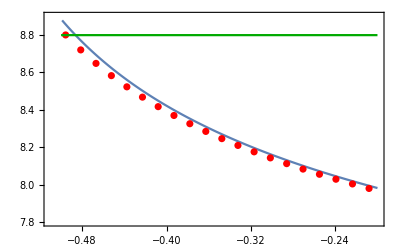

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.51,-0.2},{8.9,7.8}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black}],ListPlot[{dataT},PlotStyle->Red],Plot[8.8,{x,-0.5,-0.2},PlotStyle->{Darker[Green]}],Axes->False]
```

#### Critical coupling

```mathematica
g=1; (*coupling*)
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst]}],{en,-0.499,-0.2,0.0001}];
```

```mathematica
datarho={{-25.065638210552102, 1.5600295120375813},
{-24.9266062709746, 2.7552032101213633},
{-24.54207696609342, 2.4623932555636125},
{-24.119460305254417, 2.277259292455981},
{-23.667254839115376, 2.1492130482094955},
{-23.191101210236386, 2.053300930085953},
{-22.6947970086585, 1.9778960990228855},
{-22.181115572661405, 1.916534385410757},
{-21.652175288404045, 1.8653047506622153},
{-21.10965019147133, 1.8216768981468228},
{-20.55489769458574, 1.783929632977769},
{-19.989041148917607, 1.7508447605323743},
{-19.41302572991727, 1.721531966008557},
{-18.827657704421718, 1.6953230589276007},
{-18.233632873423364, 1.6717052289607448},
{-17.63155770444426 ,1.650277340760498},
{-17.021965374325006 ,1.630720406099696},
{-16.405328175803184 ,1.6127770907671097},
{-15.782067267712957 ,1.5962371554723576},
{-15.152560446577061 ,1.580926898097596},
{-14.51714841905515 ,1.566701357298795},
{-13.876139921202668 ,1.5534384612775232},
{-13.229815938583178 ,1.5410345721525633},
{-12.578433216739782, 1.5294010482971363},
{-11.922227205404152, 1.5184615603415548},
{-11.261414546320097, 1.5081499727800654},
{-10.596195189870883, 1.498408655319766},
{-9.926754207267024 ,1.4891871244822652},
{-9.253263351119639, 1.4804409416407378}};
dataT=Table[{datarho[[i,1]]/R,2π*datarho[[i,2]]},{i,1,25}];
```

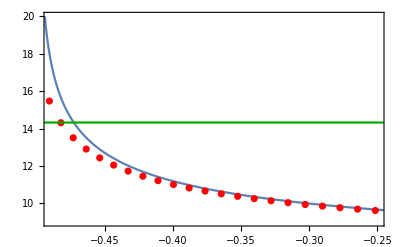

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.49,-0.25},{20,9}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black}],ListPlot[{dataT},PlotStyle->Red],Plot[14.32,{x,-0.5,-0.2},PlotStyle->{Darker[Green]}],Axes->False]
```

#### Superradiant phase

```mathematica
g=2^(1/2);
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,4}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
qtp3=qtpsort[[3]];
qtp4=qtpsort[[4]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
rhoinst2=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp3,qtp4}];
AppendTo[rho1,{en,Re[rhoinst1]+Re[rhoinst2]}],{en,-0.625,-0.5005,0.001}];
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst1]}],{en,-0.4995,-0.2,0.001}];
```

```mathematica
datarho={{-30.891219305606548, 2.339116336015177},
{-30.891219304822442 ,2.339116331809754},
{-30.042606361816283 ,2.374726789598573},
{-30.04260632313772 ,2.3747265802338067},
{-29.208146602107497, 2.419206449477698},
{-29.208145386187503, 2.419199776901384},
{-28.39109038102518 ,2.4771020727147905},
{-27.59651813942446, 2.5583645664242236},
{-27.596069245779177, 2.555768549240035},
{-26.835078634122155, 2.698583363192221},
{-26.139603353463578, 3.077770815854143},
{-25.544569996233818, 3.7020189424307475},
{-24.952396427374424, 3.105101212445147},
{-24.446071745060838, 2.713350941275739},
{-24.060901143654462, 2.488842358413719},
{-23.654112747526938, 2.428460195501803},
{-23.234891064430975, 2.343787721105261},
{-22.80257564639137 ,2.283256008505624},
{-22.359124442580168, 2.227511962185642},
{-21.905244461024246, 2.179463133008029},
{-21.441783798119616, 2.1363288236515587},
{-20.96936790936584, 2.097583602242154},
{-20.488560808566255, 2.0623865403402117},
{-19.999845597197996, 2.0302290361757263},
{-19.50365162492602 ,2.000669504046086}};
dataT=Table[{datarho[[i,1]]/R,2π*datarho[[i,2]]},{i,1,25}];
```

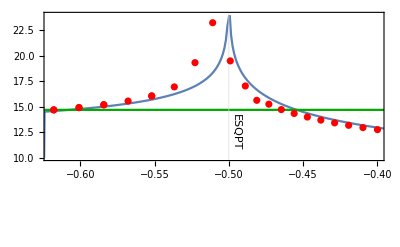

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{-.5},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-0.62,-0.4},{10,24}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black},
Epilog->{Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.495,12.5}],Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.575,4.0}]}],Plot[14.7,{x,-0.625,-0.35},PlotStyle->{Darker[Green]}],ListPlot[{dataT},PlotStyle->Red],Axes->False]
```

#### Deep superradiant phase

```mathematica
g=2;
rho1={};
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,4}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
qtp3=qtpsort[[3]];
qtp4=qtpsort[[4]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
rhoinst2=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp3,qtp4}];
AppendTo[rho1,{en,Re[rhoinst1]+Re[rhoinst2]}],{en,-1.05,-0.5005,0.001}];
Do[
qtps={};
sol= NSolve[V[q,g,0.0]==en,q];
Do[
qtp=q/.sol[[i]];
AppendTo[qtps,qtp],{i,1,2}];
qtpsort=Sort[qtps];
qtp1=qtpsort[[1]];
qtp2=qtpsort[[2]];
rhoinst1=NIntegrate[(2/(en-V[q,g,0.0]))^(1/2),{q,qtp1,qtp2}];
AppendTo[rho1,{en,Re[rhoinst1]}],{en,-0.4995,-0.2,0.001}];
```

```mathematica
datarho={{-52.65744059872463,1.033899661890845},{-51.69077266916237,1.035063807397849},{-50.72522477180006,1.0362997339666449},{-49.76086418269499,1.0376141380313815},{-48.797764285076276,1.0390145840088376},{-47.836005341098016,1.0405096525929425},{-46.875675392672875,1.0421091212506064},{-45.916871318973605,1.0438241855676083},{-44.95970008552635,1.0456677329113444},{-44.00428022953735,1.0476546837939618},{-43.05074363912337,1.049802421834847},{-42.09923770180578,1.0521313411010307},{-41.149927922002455,1.0546655510867606},{-40.20300114135195,1.0574337965465754},{-39.25866954415664,1.0604706748571215},{-38.317175699785196,1.0638182715679751},{-37.37879899248719,1.0675283878299053},{-36.44386391660427,1.071665586513551},{-35.51275082135537,1.0763112443475231},{-34.58590953629165,1.081568322170682},{-33.66387514765498,1.0875647480918536},{-32.747281381490254,1.0944486805687665},{-31.83685884935374,1.1023620103868748},{-30.9333971839319,1.1113823948873196},{-30.03767069559675,1.1214877853911907},{-29.15046154153787,1.1328291511918271},{-28.273252368725146,1.1472195923333393},{-27.411425556242236,1.173735198952484},{-26.58418455658336,1.2461042501534354},{-25.82404690513316,1.393195744263958},{-25.095434901843035,1.3523568863891688},{-24.29280034042861,1.154975349615663},{-23.37911519917151,1.0399865055085324},{-22.383120062120433,0.9704598466665239},{-21.322725069229712,0.9171361526564742},{-20.20397097951612,0.8717198590163457},{-19.029023184319527,0.8314362309003422},{-17.79870350008757,0.7949749267902301},{-16.513186537928785,0.7615377055956707},{-15.172224853045828,0.7305718552658225},{-13.775243822521338,0.7016700339517116},{-12.321391130509618,0.6745207520717951},{-10.809564841400334,0.6488793682261471},{-9.238428558972306,0.6245495191603186},{-7.606417487564348,0.6013706150207437},{-5.911737383302632,0.5792091278667443},{-4.1523574627920805,0.5579523600169612},{-2.325997771081838,0.5375038844909199},{-0.43011110544244396,0.5177801401492589}};
dataT=Table[{datarho[[i,1]]/R,4π*datarho[[i,2]]},{i,1,Length[datarho]}];
```

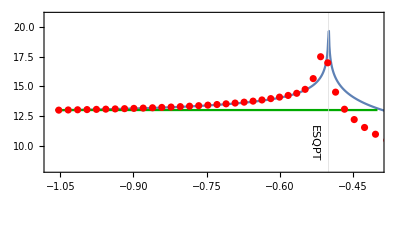

```mathematica
Tc=Show[ListPlot[rho1,Joined->True,GridLines->{{-.5},{}},GridLinesStyle->{{Dashed,Thick},{}},PlotRange->{{-1.07,-0.4},{8,21}},GridLinesStyle->Red,Frame->True,LabelStyle->{15,Black},Epilog->{Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.53,10.2}],Inset[Rotate[Text[Style["ESQPT",Black,14]],-90 Degree],{-0.575,4.0}]}],Plot[13,{x,-1.06,-0.4},PlotStyle->{Darker[Green]}],ListPlot[{dataT},PlotStyle->Red],Axes->False]
```

```mathematica
Export["Period_QRM_resonant4.png",Tc]
```

Period_QRM_resonant4.png